```mathematica
b=2;
c=3/2;
cO=0.9;
cB=1.8;

fitO[o_,y_,B_]:=o+(b-c)*y+b*B;
fitY[o_,y_,B_]:=(b-cO)*o+y+(b-cB)*B;
fitB[o_,y_,B_]:=o*(b-c)+b*y+B;

fitmedio[o_,y_,B_]:=fitO[o,y,B]*o+fitY[o,y,B]*y+fitB[o,y,B]*B;

dodt[o_,y_,B_]:=o*(fitO[o,y,B]-fitmedio[o,y,B]);
dydt[o_,y_,B_]:=y*(fitY[o,y,B]-fitmedio[o,y,B]);
dbdt[o_,y_,B_]:=B*(fitB[o,y,B]-fitmedio[o,y,B]);

dodt2[o_,y_]:=dodt[o,y,1-o-y];
dydt2[o_,y_]:=dydt[o,y,1-o-y];
```

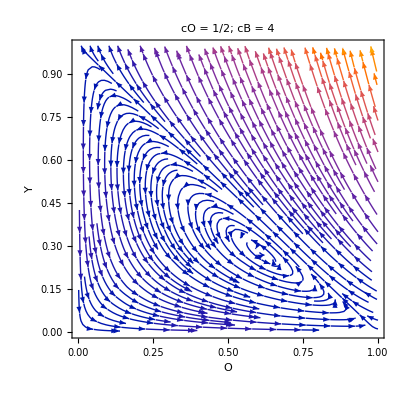

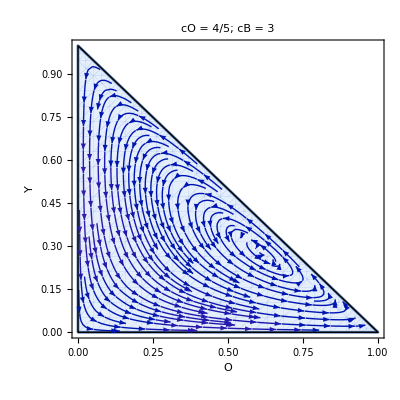

```mathematica
StreamPlot[{dodt2[o,y],dydt2[o,y]},{o,0,1},{y,0,1},StreamPoints->Fine,FrameLabel->{"O","Y"},PlotTheme->"Detailed",PlotRangePadding->None, PlotLabel->"cO = 1/2; cB = 4"]

StreamPlot[{dodt2[o,y],dydt2[o,y]},{o,0,1},{y,0,1},StreamPoints->Fine,FrameLabel->{"O","Y"},PlotTheme->"Detailed",PlotRangePadding->None,RegionFunction->Function[{o,y,u,v},o>=0&&y>=0&&o+y<=1],Epilog->{Thick,Line[{{0,0},{1,0},{0,1},{0,0}}]},PlotLabel->"cO = 4/5; cB = 3"]
```

{{o→0.,y→0.},{o→0.611111,y→0.277778},{o→1.,y→0.}}

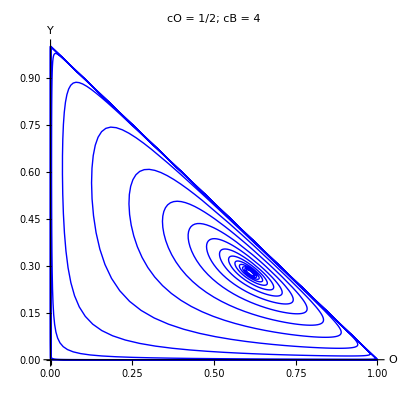

```mathematica
equilibria=FindInstance[{dodt2[o,y]==0,dydt2[o,y]==0,o>=0,y>=0,o+y<=1},{o,y},Reals,20]

sol=NDSolve[{o'[t]==dodt2[o[t],y[t]],y'[t]==dydt2[o[t],y[t]],o[0]== 0.62,y[0]== 0.27},{o,y},{t,0,1000}];

ParametricPlot[Evaluate[{o[t],y[t]}/. sol],{t,0,1000},PlotRange->{{0,1},{0,1}},PlotStyle->{Thick,Blue},AxesLabel->{"O","Y"}, PlotLabel->"cO = 1/2; cB = 4"]
```

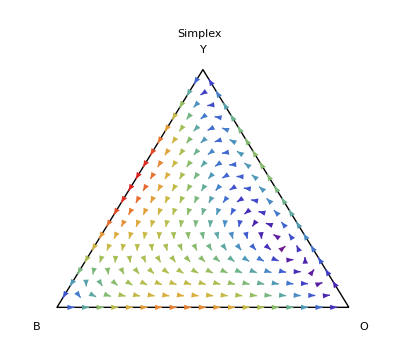

```mathematica
(*Vértices do triângulo*)
vO={1,0};
vY={1/2,Sqrt[3]/2};
vB={0,0};

maxNorm=Max[Flatten[Table[Norm[{dodt2[o,y],dydt2[o,y]}],{o,0,1,0.02},{y,0,1-o,0.02}]]];

colorFunc[o_,y_]:=ColorData["Rainbow"][Norm[{dodt2[o,y],dydt2[o,y]}]/maxNorm];

(*Converte (o,y)->(x,y) do triângulo*)
barycentricToCartesian[o_,y_]:=o*vO+y*vY+(1-o-y)*vB;

(*Gera setas do campo*)
field=Table[Module[{pt,vec,normvec},pt=barycentricToCartesian[o,y];
vec=barycentricToCartesian[o+dodt2[o,y],y+dydt2[o,y]]-pt;
normvec=0.01*Normalize[vec];
{colorFunc[o,y],Arrow[{pt,pt+normvec}]}],{o,0,1,0.05},{y,0,1-o,0.05}];

(*Desenha triângulo e campo*)
Graphics[
{(*Triângulo*)
Thick,Line[{vO,vY,vB,vO}],
Text["O",vO+{0.05,-0.07}],
Text["Y",vY+{0,0.07}],
Text["B",vB+{-0.07,-0.07}],
(*Campo de setas*)
field},
Axes->False,AspectRatio->Automatic,PlotLabel->"Simplex"]
```

{{o→0,y→0},{o→0,y→1},{o→11/18,y→5/18},{o→1,y→0}}

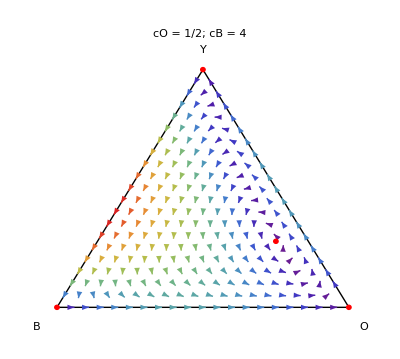

```mathematica
equilibria=FindInstance[{dodt2[o,y]==0,dydt2[o,y]==0,o>=0,y>=0,o+y<=1},{o,y},Reals,20]

(*Vértices do triângulo*)
vO={1,0};
vY={1/2,Sqrt[3]/2};
vB={0,0};

maxNorm=Max[Flatten[Table[Norm[{dodt2[o,y],dydt2[o,y]}],{o,0,1,0.02},{y,0,1-o,0.02}]]];

colorFunc[o_,y_]:=ColorData["Rainbow"][Norm[{dodt2[o,y],dydt2[o,y]}]/maxNorm];

(*Converte (o,y)->(x,y) do triângulo*)
barycentricToCartesian[o_,y_]:=o*vO+y*vY+(1-o-y)*vB;

(*Gera setas do campo*)
field=Table[Module[{pt,vec,normvec},pt=barycentricToCartesian[o,y];
vec=barycentricToCartesian[o+dodt2[o,y],y+dydt2[o,y]]-pt;
normvec=0.01*Normalize[vec];
{colorFunc[o,y],Arrow[{pt,pt+normvec}]}],{o,0,1,0.05},{y,0,1-o,0.05}];

equilibriaRaw={{o->0,y->0},{o->0,y->1},equilibria[[3]],{o->1,y->0}};
equilibriaList=equilibriaRaw/. {o->x_,y->y_}:>{x,y};
eqPoints=barycentricToCartesian@@@equilibriaList;
eqMarkers={Red,Disk[#,0.01]&/@eqPoints};

(*Desenha triângulo e campo*)
Graphics[
{(*Triângulo*)
Thick,Line[{vO,vY,vB,vO}],
Text["O",vO+{0.05,-0.07}],
Text["Y",vY+{0,0.07}],
Text["B",vB+{-0.07,-0.07}],
(*Campo de setas*)
field, 
eqMarkers},
Axes->False,AspectRatio->Automatic,PlotLabel->"cO = 1/2; cB = 4"]
```